## Minimierung der Rosebrock - Funktion mittels des Trust-Region-Verfahrens

```mathematica
(* Die Parameter *)
γ1=0.5;
γ2=2;
η1=0.1;
η2=0.9;
β=2;
α = 0.5;
ϵ=10^(-3);
```

```mathematica
(* Cauchy-Schritt(sc = tau * sl) und Newton-Schritt sn *)
Tau[G_,H_,Δ_]:=If[G.H.G ≤ 0, 1, Min[(Norm[G]^3)/(Δ*G.H.G) ,1]];
CauchySchritt[G_,H_,Δ_]:= -Tau[G,H,Δ]*((Δ*G)/(Norm[G]));
NewtonSchritt[G_,H_]:=-Inverse[H].G;
(* Die Cauchy-Abstiegsbedingung entscheidet, ob Newton- oder Cauchy-Schritt gewählt werden muss. Zusätzlich werden diese Schritte auch jeweils mit C für Cauchy- und mit N für Newton-Schritt benennt. *)
CABedingung[G_,H_,N_, C_,Δ_]:=Module[{Tmp,Tmp2},
Tmp=If[(-G.N - 0.5*N.H.N ≥α*(-G.C - 0.5*C.H.C)),
Tmp2="N";N,
Tmp2="C";C];
Tmp=If[Norm[Tmp]≤β Δ,Tmp,C];
{Tmp,Tmp2}
];
(* Rho dient für die Bewertung der Qualität des berechneten Schrittes *)
Rho[x_,s_,G_,H_,f_]:=(f[x]-f[x+ s])/(-G.s - 0.5*s.H.s);
(* Je nach Rho ρ wird entweder der Radius Δ verkleinert, beibehalten oder vergrößert *)
UpdateTrustRegion[Δ_,rho_]:=Module[{Δout},
If[rho≤η1,Δout=γ1 Δ];
If[η1<rho≤η2,Δout=0.75Δ];
If[η2<rho,Δout=γ2 Δ];
Δout];
(* Ist Rho ρ mindestens größer als η1, so wird der Schritt akzeptiert *)
AkzeptiereSchritt[x_,s_,rho_]:=If[rho>η1, x+s, x];

(* An das Verfahren wird eine Testfunktion f, ein Startwert x0 und höchstanzahl an Iterationen n übergeben. Zuerst werden die erste und zweite Ableitungen, bzw. G und H, der Tesfunktion f an der Stelle x berechnet. Diese werden dann später an oben aufgeführen Definitionen übergeben und an der Stelle x ausgewärtet. Zunächst werden Cauchy- und Newton-Schritt berechnet und mit Hilfe von Cauchy-Abstiegsbedingung geprüft, welche der beiden gewählt werden muss. Danach wird Rho berechnet und mit AkzeptiereSchritt geprüft, ob die neue x^(k+1) die Anforderung genügt. Zuletzt wird mit UpdateTrustRegion die am Anfang als Δ=2 festgesetzte Radius aktualisiert. *)
TrustRegionVerfahren[f_,x0_, n_]:=Module[{G,H,x=x0,X = {x0},s,Δ=2,rho,k,x01,x02,Gnow,Hnow,Taunow,Cnow,Nnow,Kind},
G[{x1_,x2_}]:=Evaluate[{D[f[{x01,x02}],x01],D[f[{x01,x02}],x02]}/.{x01->x1,x02->x2}];
H[{x1_,x2_}]:=Evaluate[{D[G[{x01,x02}],x01],D[G[{x01,x02}],x02]}/.{x01->x1,x02->x2}];
Catch[
Do[
If[Norm[G[x]]<ϵ,Throw[Print[k]]];

Gnow=G[x];
Hnow=H[x];
Taunow=Tau[x,Gnow,Hnow,Δ];
Cnow=CauchySchritt[Gnow,Hnow,Δ];
Nnow=NewtonSchritt[Gnow,Hnow];
{s,Kind}=CABedingung[Gnow,Hnow,Nnow,Cnow,Δ];
rho=Rho[x,s,Gnow,Hnow,f];
x=AkzeptiereSchritt[x,s,rho];
Δ=UpdateTrustRegion[Δ,rho];
X=Append[X,x],
 {k,0,n}];
];
X];
```

```mathematica
f[{x1_,x2_}]:=100(x2-x1^2)^2+(1-x1)^2;
X=TrustRegionVerfahren[f,x0={-1.9,2.},10000]//N
```

1192

{{-1.9,2.},{-1.89102,3.57588},{-1.88898,3.57589},{-1.88891,3.56772},{-1.88891,3.56772},{-1.88891,3.56772},{-1.88683,3.56773},{-1.88669,3.55914},{-1.88669,3.55914},{-1.88669,3.55914},{-1.88456,3.55918},{-1.88436,3.55011},{-1.88436,3.55011},{-1.88436,3.55011},{-1.88217,3.55016},{-1.88189,3.54054},{-1.88189,3.54054},{-1.88189,3.54054},{-1.87963,3.54061},{-1.87926,3.53036},{-1.87926,3.53036},{-1.87926,3.53036},{-1.87693,3.53045},{-1.87644,3.51945},{-1.87644,3.51945},{-1.87644,3.51945},{-1.87403,3.51956},{-1.87339,3.50766},{-1.87339,3.50766},{-1.87339,3.50766},{-1.87089,3.50779},{-1.87007,3.49478},{-1.87007,3.49478},{-1.87007,3.49478},{-1.87007,3.49478},{-1.86746,3.49495},{-1.8664,3.48055},{-1.8664,3.48055},{-1.8664,3.48055},{-1.86366,3.48075},{-1.86228,3.46452},{-1.86228,3.46452},{-1.86228,3.46452},{-1.85937,3.46476},{-1.85754,3.44602},{-1.85754,3.44602},{-1.85754,3.44602},{-1.85442,3.44633},{-1.85187,3.42387},{-1.85187,3.42387},{-1.85187,3.42387},{-1.84846,3.42425},{-1.84471,3.39567},{-1.84471,3.39567},{-1.84471,3.39567},{-1.84086,3.39618},{-1.83455,3.35532},{-1.83455,3.35532},{-1.83455,3.35532},{-1.83455,3.35532},{-1.82994,3.35604},{-1.81502,3.27685},{-1.81502,3.27685},{-1.81502,3.27685},{-1.80854,3.27808},{-1.80854,3.27808},{-1.80854,3.27808},{-1.68412,2.79381},{-1.67044,2.79723},{-1.66322,2.784},{-1.66602,2.78246},{-1.65938,2.77065},{-1.66203,2.76915},{-1.65583,2.75843},{-1.65836,2.75696},{-1.65252,2.74712},{-1.65496,2.74566},{-1.64942,2.73654},{-1.65177,2.7351},{-1.64648,2.72657},{-1.64876,2.72515},{-1.64369,2.71714},{-1.64591,2.71573},{-1.64103,2.70816},{-1.64319,2.70677},{-1.63848,2.69959},{-1.64058,2.6982},{-1.63602,2.69136},{-1.63808,2.68998},{-1.63365,2.68345},{-1.63567,2.68208},{-1.63137,2.67583},{-1.63335,2.67446},{-1.62915,2.66846},{-1.63109,2.66709},{-1.627,2.66132},{-1.62891,2.65996},{-1.62491,2.65439},{-1.62679,2.65303},{-1.62287,2.64766},{-1.62472,2.6463},{-1.62088,2.6411},{-1.62271,2.63975},{-1.61894,2.63472},{-1.62074,2.63337},{-1.61705,2.62848},{-1.61882,2.62713},{-1.61519,2.62239},{-1.61695,2.62105},{-1.61338,2.61644},{-1.61511,2.61509},{-1.61159,2.61061},{-1.61331,2.60926},{-1.60985,2.60489},{-1.61154,2.60355},{-1.60813,2.59929},{-1.6098,2.59794},{-1.60644,2.59379},{-1.6081,2.59244},{-1.60478,2.58839},{-1.60642,2.58704},{-1.60315,2.58308},{-1.60477,2.58173},{-1.60154,2.57786},{-1.60315,2.57651},{-1.59995,2.57272},{-1.60155,2.57137},{-1.59839,2.56766},{-1.59997,2.56631},{-1.59685,2.56268},{-1.59842,2.56132},{-1.59533,2.55777},{-1.59688,2.55641},{-1.59382,2.55292},{-1.59537,2.55156},{-1.59234,2.54814},{-1.59387,2.54678},{-1.59087,2.54343},{-1.59239,2.54206},{-1.58943,2.53877},{-1.59093,2.53741},{-1.58799,2.53417},{-1.58949,2.5328},{-1.58658,2.52962},{-1.58806,2.52825},{-1.58517,2.52513},{-1.58665,2.52376},{-1.58379,2.52069},{-1.58525,2.51931},{-1.58241,2.51629},{-1.58387,2.51492},{-1.58105,2.51194},{-1.5825,2.51056},{-1.5797,2.50764},{-1.58114,2.50626},{-1.57836,2.50338},{-1.57979,2.50199},{-1.57704,2.49916},{-1.57846,2.49777},{-1.57572,2.49498},{-1.57714,2.49359},{-1.57442,2.49083},{-1.57583,2.48944},{-1.57313,2.48673},{-1.57453,2.48533},{-1.57185,2.48266},{-1.57324,2.48126},{-1.57057,2.47862},{-1.57195,2.47722},{-1.56931,2.47462},{-1.57068,2.47322},{-1.56805,2.47065},{-1.56942,2.46924},{-1.56681,2.46671},{-1.56817,2.4653},{-1.56557,2.46281},{-1.56692,2.46139},{-1.56434,2.45893},{-1.56569,2.45751},{-1.56312,2.45508},{-1.56446,2.45365},{-1.5619,2.45125},{-1.56324,2.44982},{-1.5607,2.44745},{-1.56203,2.44602},{-1.5595,2.44368},{-1.56082,2.44225},{-1.5583,2.43993},{-1.55962,2.43849},{-1.55712,2.43621},{-1.55843,2.43477},{-1.55594,2.43251},{-1.55724,2.43106},{-1.55476,2.42883},{-1.55607,2.42738},{-1.5536,2.42518},{-1.55489,2.42372},{-1.55243,2.42154},{-1.55372,2.42008},{-1.55128,2.41793},{-1.55256,2.41646},{-1.55013,2.41433},{-1.55141,2.41286},{-1.54898,2.41076},{-1.55026,2.40928},{-1.54784,2.4072},{-1.54911,2.40572},{-1.54671,2.40366},{-1.54797,2.40218},{-1.54557,2.40014},{-1.54683,2.39865},{-1.54445,2.39664},{-1.5457,2.39514},{-1.54333,2.39315},{-1.54458,2.39165},{-1.54221,2.38968},{-1.54345,2.38817},{-1.54109,2.38622},{-1.54234,2.38471},{-1.53998,2.38278},{-1.54122,2.38127},{-1.53888,2.37935},{-1.54011,2.37783},{-1.53778,2.37594},{-1.53901,2.37442},{-1.53668,2.37254},{-1.5379,2.37101},{-1.53558,2.36916},{-1.5368,2.36762},{-1.53449,2.36579},{-1.53571,2.36425},{-1.5334,2.36243},{-1.53462,2.36088},{-1.53232,2.35908},{-1.53353,2.35753},{-1.53124,2.35575},{-1.53244,2.35419},{-1.53016,2.35242},{-1.53136,2.35086},{-1.52908,2.34911},{-1.53028,2.34754},{-1.52801,2.34581},{-1.5292,2.34423},{-1.52693,2.34252},{-1.52813,2.34094},{-1.52587,2.33924},{-1.52705,2.33765},{-1.5248,2.33596},{-1.52598,2.33437},{-1.52374,2.3327},{-1.52492,2.3311},{-1.52267,2.32945},{-1.52385,2.32784},{-1.52161,2.3262},{-1.52279,2.32459},{-1.52056,2.32297},{-1.52173,2.32135},{-1.5195,2.31974},{-1.52067,2.31812},{-1.51845,2.31652},{-1.51961,2.31489},{-1.51739,2.31331},{-1.51856,2.31167},{-1.51634,2.3101},{-1.5175,2.30846},{-1.51529,2.30691},{-1.51645,2.30525},{-1.51425,2.30372},{-1.5154,2.30206},{-1.5132,2.30053},{-1.51435,2.29887},{-1.51215,2.29735},{-1.5133,2.29568},{-1.51111,2.29418},{-1.51225,2.2925},{-1.51007,2.29101},{-1.51121,2.28933},{-1.50903,2.28785},{-1.51016,2.28616},{-1.50798,2.2847},{-1.50912,2.283},{-1.50694,2.28155},{-1.50808,2.27984},{-1.50591,2.2784},{-1.50704,2.27668},{-1.50487,2.27526},{-1.50599,2.27354},{-1.50383,2.27212},{-1.50495,2.27039},{-1.50279,2.26899},{-1.50391,2.26725},{-1.50176,2.26586},{-1.50288,2.26411},{-1.50072,2.26273},{-1.50184,2.26098},{-1.49968,2.25961},{-1.5008,2.25785},{-1.49865,2.25649},{-1.49976,2.25472},{-1.49761,2.25337},{-1.49872,2.25159},{-1.49658,2.25026},{-1.49768,2.24847},{-1.49554,2.24715},{-1.49665,2.24535},{-1.49451,2.24404},{-1.49561,2.24223},{-1.49347,2.24093},{-1.49457,2.23912},{-1.49244,2.23783},{-1.49353,2.236},{-1.4914,2.23472},{-1.4925,2.23289},{-1.49036,2.23162},{-1.49146,2.22978},{-1.48933,2.22852},{-1.49042,2.22667},{-1.48829,2.22542},{-1.48938,2.22356},{-1.48725,2.22232},{-1.48834,2.22045},{-1.48622,2.21922},{-1.4873,2.21734},{-1.48518,2.21612},{-1.48626,2.21423},{-1.48414,2.21302},{-1.48522,2.21112},{-1.4831,2.20992},{-1.48417,2.20801},{-1.48206,2.20682},{-1.48313,2.2049},{-1.48102,2.20372},{-1.48209,2.20179},{-1.47997,2.20062},{-1.48104,2.19868},{-1.47893,2.19751},{-1.48,2.19556},{-1.47788,2.19441},{-1.47895,2.19245},{-1.47684,2.1913},{-1.4779,2.18933},{-1.47579,2.1882},{-1.47685,2.18622},{-1.47474,2.18509},{-1.4758,2.1831},{-1.47369,2.18198},{-1.47474,2.17997},{-1.47264,2.17886},{-1.47369,2.17685},{-1.47158,2.17575},{-1.47263,2.17372},{-1.47053,2.17263},{-1.47158,2.17059},{-1.46947,2.16951},{-1.47052,2.16746},{-1.46841,2.16638},{-1.46945,2.16432},{-1.46735,2.16325},{-1.46839,2.16118},{-1.46628,2.16012},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46732,2.15803},{-1.46522,2.15698},{-1.46626,2.15488},{-1.46626,2.15488},{-1.46626,2.15488},{-1.46626,2.15488},{-1.46415,2.15384},{-1.46519,2.15173},{-1.46519,2.15173},{-1.46519,2.15173},{-1.46519,2.15173},{-1.46308,2.1507},{-1.46411,2.14857},{-1.46411,2.14857},{-1.46411,2.14857},{-1.46411,2.14857},{-1.46201,2.14755},{-1.46304,2.14541},{-1.46304,2.14541},{-1.46304,2.14541},{-1.46093,2.14439},{-1.46196,2.14224},{-1.46196,2.14224},{-1.46196,2.14224},{-1.45985,2.14123},{-1.46088,2.13907},{-1.46088,2.13907},{-1.46088,2.13907},{-1.46088,2.13907},{-1.45877,2.13806},{-1.4598,2.13589},{-1.4598,2.13589},{-1.4598,2.13589},{-1.45769,2.13489},{-1.45871,2.1327},{-1.45871,2.1327},{-1.45871,2.1327},{-1.4566,2.13172},{-1.45762,2.12951},{-1.45762,2.12951},{-1.45762,2.12951},{-1.45551,2.12853},{-1.45653,2.12631},{-1.45653,2.12631},{-1.45653,2.12631},{-1.45442,2.12534},{-1.45544,2.12311},{-1.45544,2.12311},{-1.45544,2.12311},{-1.45332,2.12214},{-1.45434,2.11989},{-1.45434,2.11989},{-1.45434,2.11989},{-1.45434,2.11989},{-1.45223,2.11894},{-1.45324,2.11667},{-1.45324,2.11667},{-1.45324,2.11667},{-1.45112,2.11573},{-1.45214,2.11345},{-1.45214,2.11345},{-1.45214,2.11345},{-1.45002,2.11251},{-1.45103,2.11021},{-1.45103,2.11021},{-1.45103,2.11021},{-1.44891,2.10928},{-1.44992,2.10697},{-1.44992,2.10697},{-1.44992,2.10697},{-1.4478,2.10605},{-1.4488,2.10372},{-1.4488,2.10372},{-1.4488,2.10372},{-1.44668,2.1028},{-1.44768,2.10046},{-1.44768,2.10046},{-1.44768,2.10046},{-1.44556,2.09955},{-1.44656,2.09719},{-1.44656,2.09719},{-1.44656,2.09719},{-1.44443,2.09629},{-1.44543,2.09391},{-1.44543,2.09391},{-1.44543,2.09391},{-1.44331,2.09302},{-1.4443,2.09062},{-1.4443,2.09062},{-1.4443,2.09062},{-1.44217,2.08974},{-1.44317,2.08732},{-1.44317,2.08732},{-1.44317,2.08732},{-1.44317,2.08732},{-1.44103,2.08644},{-1.44203,2.08401},{-1.44203,2.08401},{-1.44203,2.08401},{-1.43989,2.08314},{-1.44088,2.08069},{-1.44088,2.08069},{-1.44088,2.08069},{-1.43875,2.07983},{-1.43973,2.07736},{-1.43973,2.07736},{-1.43973,2.07736},{-1.43759,2.07651},{-1.43858,2.07402},{-1.43858,2.07402},{-1.43858,2.07402},{-1.43644,2.07317},{-1.43742,2.07066},{-1.43742,2.07066},{-1.43742,2.07066},{-1.43528,2.06982},{-1.43626,2.06729},{-1.43626,2.06729},{-1.43626,2.06729},{-1.43411,2.06646},{-1.43509,2.06391},{-1.43509,2.06391},{-1.43509,2.06391},{-1.43294,2.06309},{-1.43391,2.06052},{-1.43391,2.06052},{-1.43391,2.06052},{-1.43176,2.0597},{-1.43273,2.05711},{-1.43273,2.05711},{-1.43273,2.05711},{-1.43057,2.05631},{-1.43154,2.05369},{-1.43154,2.05369},{-1.43154,2.05369},{-1.42939,2.05289},{-1.43035,2.05026},{-1.43035,2.05026},{-1.43035,2.05026},{-1.42819,2.04946},{-1.42915,2.04681},{-1.42915,2.04681},{-1.42915,2.04681},{-1.42699,2.04602},{-1.42795,2.04334},{-1.42795,2.04334},{-1.42795,2.04334},{-1.42578,2.04256},{-1.42674,2.03986},{-1.42674,2.03986},{-1.42674,2.03986},{-1.42457,2.03909},{-1.42552,2.03636},{-1.42552,2.03636},{-1.42552,2.03636},{-1.42334,2.0356},{-1.4243,2.03285},{-1.4243,2.03285},{-1.4243,2.03285},{-1.4243,2.03285},{-1.42212,2.03209},{-1.42307,2.02932},{-1.42307,2.02932},{-1.42307,2.02932},{-1.42088,2.02857},{-1.42183,2.02577},{-1.42183,2.02577},{-1.42183,2.02577},{-1.41964,2.02503},{-1.42058,2.0222},{-1.42058,2.0222},{-1.42058,2.0222},{-1.41839,2.02147},{-1.41933,2.01861},{-1.41933,2.01861},{-1.41933,2.01861},{-1.41713,2.01789},{-1.41807,2.01501},{-1.41807,2.01501},{-1.41807,2.01501},{-1.41586,2.01429},{-1.4168,2.01138},{-1.4168,2.01138},{-1.4168,2.01138},{-1.41459,2.01067},{-1.41552,2.00773},{-1.41552,2.00773},{-1.41552,2.00773},{-1.4133,2.00703},{-1.41423,2.00406},{-1.41423,2.00406},{-1.41423,2.00406},{-1.41201,2.00337},{-1.41294,2.00037},{-1.41294,2.00037},{-1.41294,2.00037},{-1.41071,1.99968},{-1.41163,1.99665},{-1.41163,1.99665},{-1.41163,1.99665},{-1.4094,1.99597},{-1.41032,1.99291},{-1.41032,1.99291},{-1.41032,1.99291},{-1.40808,1.99224},{-1.40899,1.98915},{-1.40899,1.98915},{-1.40899,1.98915},{-1.40675,1.98849},{-1.40766,1.98536},{-1.40766,1.98536},{-1.40766,1.98536},{-1.40541,1.98471},{-1.40632,1.98155},{-1.40632,1.98155},{-1.40632,1.98155},{-1.40406,1.9809},{-1.40496,1.9777},{-1.40496,1.9777},{-1.40496,1.9777},{-1.4027,1.97706},{-1.4036,1.97383},{-1.4036,1.97383},{-1.4036,1.97383},{-1.40132,1.9732},{-1.40222,1.96994},{-1.40222,1.96994},{-1.40222,1.96994},{-1.39994,1.96931},{-1.40083,1.96601},{-1.40083,1.96601},{-1.40083,1.96601},{-1.39854,1.96539},{-1.39943,1.96205},{-1.39943,1.96205},{-1.39943,1.96205},{-1.39713,1.96144},{-1.39801,1.95806},{-1.39801,1.95806},{-1.39801,1.95806},{-1.39571,1.95746},{-1.39659,1.95403},{-1.39659,1.95403},{-1.39659,1.95403},{-1.39427,1.95344},{-1.39515,1.94997},{-1.39515,1.94997},{-1.39515,1.94997},{-1.39283,1.94939},{-1.39369,1.94588},{-1.39369,1.94588},{-1.39369,1.94588},{-1.39369,1.94588},{-1.39136,1.9453},{-1.39222,1.94174},{-1.39222,1.94174},{-1.39222,1.94174},{-1.38988,1.94118},{-1.39074,1.93757},{-1.39074,1.93757},{-1.39074,1.93757},{-1.38839,1.93702},{-1.38924,1.93336},{-1.38924,1.93336},{-1.38924,1.93336},{-1.38688,1.93282},{-1.38773,1.92911},{-1.38773,1.92911},{-1.38773,1.92911},{-1.38536,1.92857},{-1.38619,1.92482},{-1.38619,1.92482},{-1.38619,1.92482},{-1.38381,1.92429},{-1.38464,1.92048},{-1.38464,1.92048},{-1.38464,1.92048},{-1.38225,1.91996},{-1.38308,1.91609},{-1.38308,1.91609},{-1.38308,1.91609},{-1.38067,1.91558},{-1.38149,1.91166},{-1.38149,1.91166},{-1.38149,1.91166},{-1.37907,1.91116},{-1.37988,1.90718},{-1.37988,1.90718},{-1.37988,1.90718},{-1.37746,1.90668},{-1.37826,1.90264},{-1.37826,1.90264},{-1.37826,1.90264},{-1.37582,1.90216},{-1.37661,1.89805},{-1.37661,1.89805},{-1.37661,1.89805},{-1.37416,1.89758},{-1.37494,1.8934},{-1.37494,1.8934},{-1.37494,1.8934},{-1.37247,1.89294},{-1.37325,1.88869},{-1.37325,1.88869},{-1.37325,1.88869},{-1.37076,1.88824},{-1.37153,1.88392},{-1.37153,1.88392},{-1.37153,1.88392},{-1.36903,1.88348},{-1.36979,1.87909},{-1.36979,1.87909},{-1.36979,1.87909},{-1.36727,1.87866},{-1.36802,1.87418},{-1.36802,1.87418},{-1.36802,1.87418},{-1.36549,1.87376},{-1.36622,1.86921},{-1.36622,1.86921},{-1.36622,1.86921},{-1.36367,1.8688},{-1.3644,1.86416},{-1.3644,1.86416},{-1.3644,1.86416},{-1.36183,1.86376},{-1.36254,1.85903},{-1.36254,1.85903},{-1.36254,1.85903},{-1.35996,1.85864},{-1.36065,1.85381},{-1.36065,1.85381},{-1.36065,1.85381},{-1.35805,1.85344},{-1.35873,1.84851},{-1.35873,1.84851},{-1.35873,1.84851},{-1.3561,1.84815},{-1.35677,1.84312},{-1.35677,1.84312},{-1.35677,1.84312},{-1.35412,1.84277},{-1.35477,1.83762},{-1.35477,1.83762},{-1.35477,1.83762},{-1.3521,1.83729},{-1.35274,1.83203},{-1.35274,1.83203},{-1.35274,1.83203},{-1.35274,1.83203},{-1.35004,1.8317},{-1.35066,1.82632},{-1.35066,1.82632},{-1.35066,1.82632},{-1.34794,1.82601},{-1.34853,1.82049},{-1.34853,1.82049},{-1.34853,1.82049},{-1.34579,1.8202},{-1.34636,1.81454},{-1.34636,1.81454},{-1.34636,1.81454},{-1.34359,1.81426},{-1.34413,1.80846},{-1.34413,1.80846},{-1.34413,1.80846},{-1.34133,1.80819},{-1.34185,1.80223},{-1.34185,1.80223},{-1.34185,1.80223},{-1.33902,1.80198},{-1.33951,1.79584},{-1.33951,1.79584},{-1.33951,1.79584},{-1.33665,1.79561},{-1.33711,1.7893},{-1.33711,1.7893},{-1.33711,1.7893},{-1.33421,1.78908},{-1.33464,1.78257},{-1.33464,1.78257},{-1.33464,1.78257},{-1.3317,1.78237},{-1.33209,1.77565},{-1.33209,1.77565},{-1.33209,1.77565},{-1.32911,1.77547},{-1.32947,1.76852},{-1.32947,1.76852},{-1.32947,1.76852},{-1.32644,1.76836},{-1.32675,1.76115},{-1.32675,1.76115},{-1.32675,1.76115},{-1.32368,1.76102},{-1.32394,1.75354},{-1.32394,1.75354},{-1.32394,1.75354},{-1.32082,1.75343},{-1.32102,1.74564},{-1.32102,1.74564},{-1.32102,1.74564},{-1.31784,1.74556},{-1.31798,1.73744},{-1.31798,1.73744},{-1.31798,1.73744},{-1.31475,1.73739},{-1.31481,1.72889},{-1.31481,1.72889},{-1.31481,1.72889},{-1.31151,1.72887},{-1.31149,1.71995},{-1.31149,1.71995},{-1.31149,1.71995},{-1.30812,1.71996},{-1.308,1.71058},{-1.308,1.71058},{-1.308,1.71058},{-1.30456,1.71062},{-1.30433,1.7007},{-1.30433,1.7007},{-1.30433,1.7007},{-1.30433,1.7007},{-1.30079,1.70078},{-1.30042,1.69023},{-1.30042,1.69023},{-1.30042,1.69023},{-1.29679,1.69036},{-1.29626,1.67908},{-1.29626,1.67908},{-1.29626,1.67908},{-1.29251,1.67926},{-1.29179,1.66711},{-1.29179,1.66711},{-1.29179,1.66711},{-1.28791,1.66734},{-1.28694,1.65415},{-1.28694,1.65415},{-1.28694,1.65415},{-1.28291,1.65445},{-1.28162,1.63995},{-1.28162,1.63995},{-1.28162,1.63995},{-1.2774,1.64032},{-1.2757,1.62415},{-1.2757,1.62415},{-1.2757,1.62415},{-1.27126,1.62462},{-1.26898,1.6062},{-1.26898,1.6062},{-1.26898,1.6062},{-1.26425,1.60679},{-1.26111,1.5852},{-1.26111,1.5852},{-1.26111,1.5852},{-1.256,1.58595},{-1.25148,1.55945},{-1.25148,1.55945},{-1.25148,1.55945},{-1.25148,1.55945},{-1.24583,1.56042},{-1.2387,1.52516},{-1.2387,1.52516},{-1.2387,1.52516},{-1.23217,1.52649},{-1.21843,1.47049},{-1.21843,1.47049},{-1.21843,1.47049},{-1.21016,1.47255},{-1.15681,1.30459},{-0.877673,0.692389},{-0.764451,0.571566},{-0.764451,0.571566},{-0.764451,0.571566},{-0.752698,0.575612},{-0.715344,0.488649},{-0.409775,0.0745426},{-0.33812,0.109191},{-0.33812,0.109191},{-0.33812,0.109191},{-0.33812,0.109191},{-0.319373,0.114902},{-0.309361,0.0888157},{-0.309361,0.0888157},{-0.309361,0.0888157},{-0.290324,0.0963718},{-0.276068,0.0671079},{-0.276068,0.0671079},{-0.276068,0.0671079},{-0.276068,0.0671079},{-0.256721,0.0770113},{-0.236151,0.043736},{-0.236151,0.043736},{-0.236151,0.043736},{-0.216576,0.0567886},{-0.186007,0.0184706},{-0.186007,0.0184706},{-0.186007,0.0184706},{-0.186007,0.0184706},{-0.166568,0.0360246},{-0.119008,-0.008183},{0.0855935,-0.0345357},{0.183157,0.0240279},{0.183157,0.0240279},{0.183157,0.0240279},{0.191718,0.0414337},{0.208165,0.0336438},{0.208165,0.0336438},{0.208165,0.0336438},{0.214618,0.0497389},{0.230749,0.0434492},{0.230749,0.0434492},{0.230749,0.0434492},{0.235572,0.0583448},{0.251379,0.0533309},{0.251379,0.0533309},{0.251379,0.0533309},{0.254922,0.0671457},{0.27042,0.0632303},{0.27042,0.0632303},{0.27042,0.0632303},{0.272943,0.0760777},{0.288159,0.0731216},{0.288159,0.0731216},{0.288159,0.0731216},{0.289857,0.0851048},{0.304825,0.0829992},{0.304825,0.0829992},{0.304825,0.0829992},{0.305847,0.0942099},{0.320605,0.0928702},{0.320605,0.0928702},{0.320605,0.0928702},{0.321066,0.103389},{0.335652,0.102751},{0.335652,0.102751},{0.335652,0.102751},{0.335642,0.112649},{0.350098,0.112664},{0.568112,0.275221},{0.609221,0.36946},{0.609221,0.36946},{0.609221,0.36946},{0.641236,0.398725},{0.743986,0.542958},{0.826265,0.675944},{0.90007,0.804679},{0.947896,0.89622},{0.983646,0.966281},{0.996671,0.993183},{0.999891,0.999771},{1.,1.}}

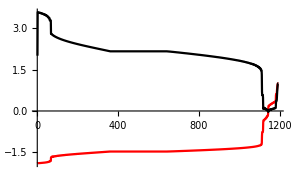

```mathematica
(* Die Iterationsverlauf der x1 und x2 *)
ListLinePlot[Transpose[X],PlotStyle->{Red,Black},PlotRange->All]
```

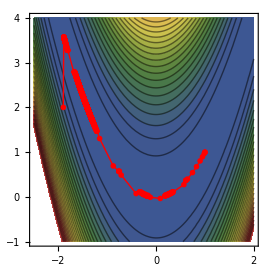

```mathematica
ContourPlot[f[{x1,x2}],{x1,-2.5,2},{x2,-1.,4},Epilog->{Red,PointSize[0.015],Map[Point,X],Line[X]},  ColorFunction->"DarkRainbow",  Contours->25]
```

```mathematica
T1=Plot3D[f[{x1,x2}],{x1,-2.5,2},{x2,-1,4}, ColorFunction->"DarkRainbow", Boxed->False, AxesLabel->Automatic, Mesh->None];
T2=Graphics3D[{PointSize[0.02],Red,Point[Table[{X[[i,1]],X[[i,2]],f[{X[[i,1]],X[[i,2]]}]},{i,1,Length[X]}]]}];
T3=Graphics3D[{Red,Line[Table[{X[[i,1]],X[[i,2]],f[{X[[i,1]],X[[i,2]]}]},{i,1,Length[X]}]]}];
Show[T1,T2,T3]
```

-Graphics3D-